```mathematica
SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem1\\my\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr}],
	Transpose[{triangles, myErr}],
	Transpose[{triangles, ostErr}]
},
PlotLegends->Placed[{"Реальна","з роботи", "Ост.-Шин."},{0.8,.5}],
Filling->xis,
PlotRange -> {0,2.5}
]
```

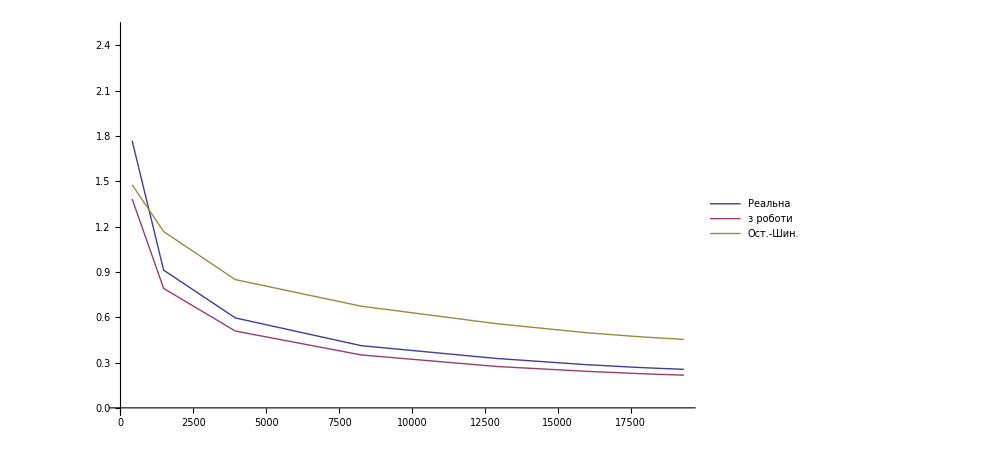
```mathematica
-Graphics-

SetDirectory["d:\\Learn\\Diploma\\DiplomaText\\include\\8NumResults\\problem1\\ost\\errors\\"];
triangles = Import["triangles.txt","List"];
realErr = Import["realError.txt","List"];
myErr = Import["myError.txt","List"];
ostErr = Import["ostError.txt","List"];

ListLinePlot[{
	Transpose[{triangles, realErr}],
	Transpose[{triangles, myErr}],
	Transpose[{triangles, ostErr}]
},
PlotLegends->Placed[{"Реальна","з роботи", "Ост.-Шин."},{0.8,.5}],
Filling->xis,
PlotRange -> {0,2.5}]
```